## 相关图的计算结果

```mathematica
SimpleGraphs[n_]:=Import["~/desktop/work_space/1 MMA/0 pkg/simplegraphs/graph"<>ToString@n<>".g6"];
Needs["IGraphM`"];
```

```mathematica
(*Graph Subscript[F, k] of 2k+1 vertices (k≥1) *)
GraphF[k_?Positive]:=Module[{vertices1,vertices2,edges},
vertices1=Range@k;
vertices2=Range[-1,-k,-1];
edges=(0<->#&)/@Join[vertices1,vertices2];
edges=Join[edges,Thread[TwoWayRule[Range@k,Range[-1,-k,-1]]]];
Graph@edges];
```

```mathematica
chk[k_]:=Module[{},
If[n≥2k+1,
m=(EdgeCount/@graphk)//Max;
Print["n=",n,",\tk=",k,"\tex(n,F_k)=",m,"\ngraphs:"];
Print[Select[graphk,EdgeCount@#==m&],"\n"]]];
```

———————— division ——————————

Vertex number: 3	{0.008786,s}

Length of isomorpic class: 4

4

4

4

3

n=3,	k=1	ex(n,F_k)=2
graphs:

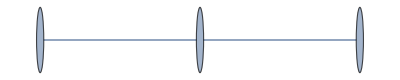

———————— division ——————————

Vertex number: 4	{0.00825,s}

Length of isomorpic class: 11

11

11

11

7

n=4,	k=1	ex(n,F_k)=4
graphs:

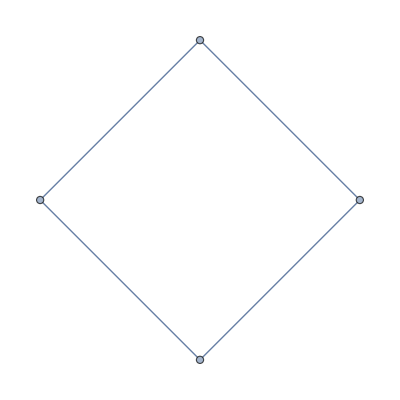

———————— division ——————————

Vertex number: 5	{0.01223,s}

Length of isomorpic class: 34

34

34

28

n=5,	k=2	ex(n,F_k)=7
graphs:

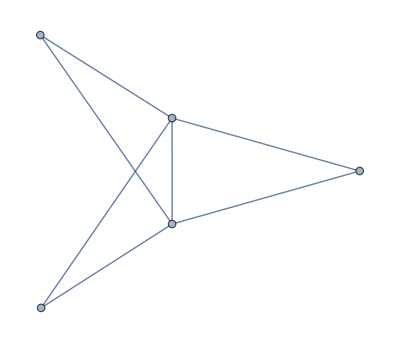
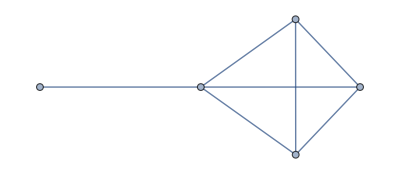
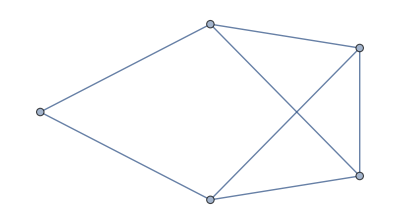

14

n=5,	k=1	ex(n,F_k)=6
graphs:

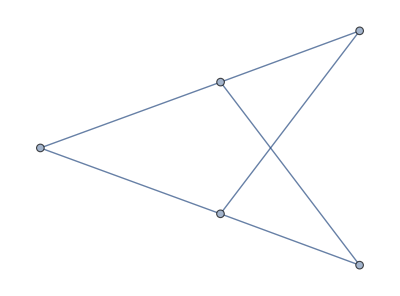

———————— division ——————————

Vertex number: 6	{0.182925,s}

Length of isomorpic class: 156

156

156

98

n=6,	k=2	ex(n,F_k)=10
graphs:

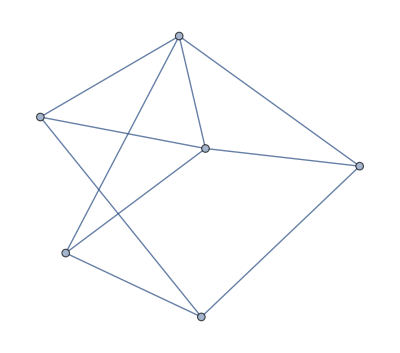

38

n=6,	k=1	ex(n,F_k)=9
graphs:

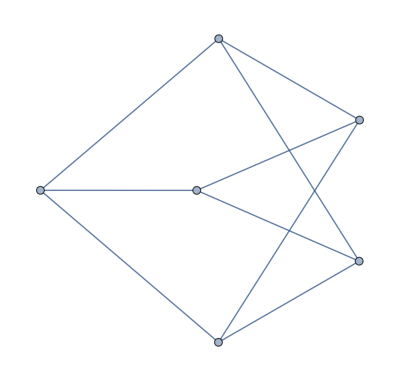

———————— division ——————————

Vertex number: 7	{0.841089,s}

Length of isomorpic class: 1044

1044

943

n=7,	k=3	ex(n,F_k)=17
graphs:

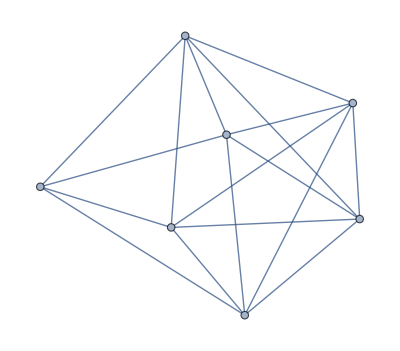

400

n=7,	k=2	ex(n,F_k)=13
graphs:

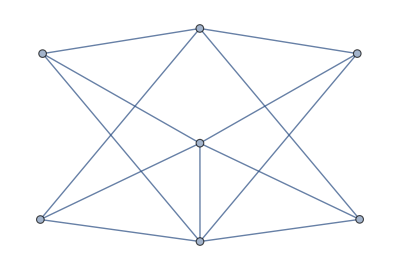
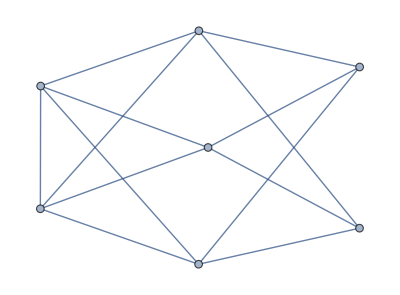

107

n=7,	k=1	ex(n,F_k)=12
graphs:

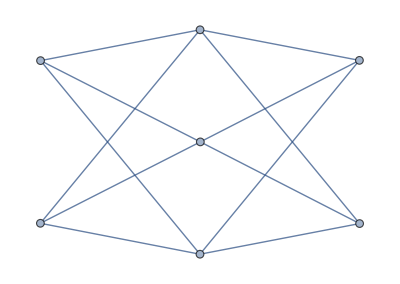

———————— division ——————————

Vertex number: 8	{2.795,s}

Length of isomorpic class: 12346

12346

8820

n=8,	k=3	ex(n,F_k)=20
graphs:

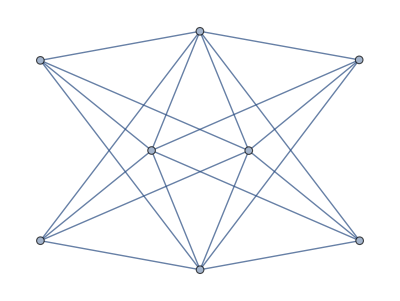
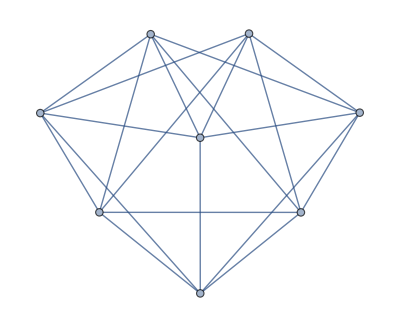
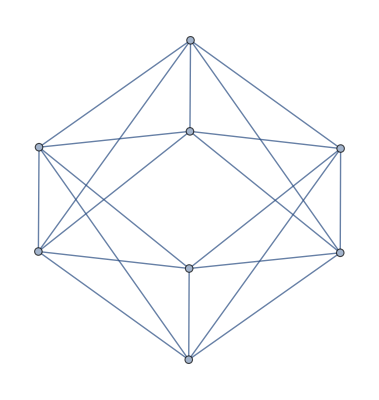
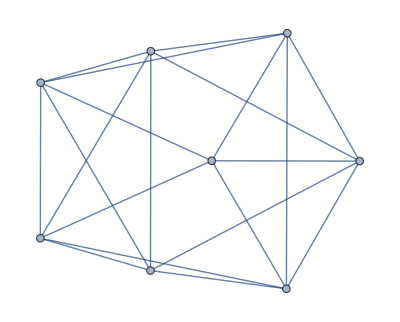

2290

n=8,	k=2	ex(n,F_k)=17
graphs:

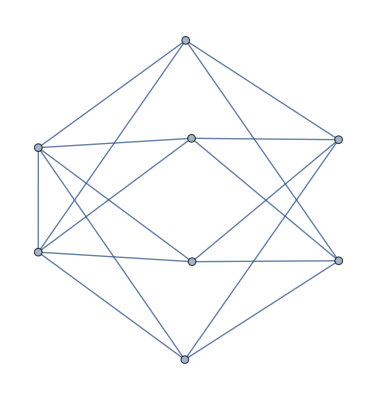

410

n=8,	k=1	ex(n,F_k)=16
graphs:

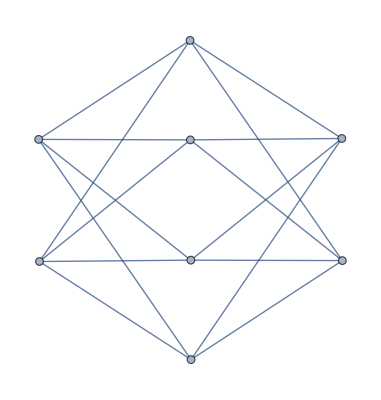

———————— division ——————————

```mathematica
For[n=3,n<10,n++,
Print["\n\n———————— division ——————————"];
Print["Vertex number: ",n,"\t",Timing[graphs=SimpleGraphs[n];"s"]];
Print["Length of isomorpic class: ",Length@graphs];
k=4;
graphk=Select[graphs,!IGSubisomorphicQ[GraphF[k],#]&];
chk[k];
k=3;
graphk=Select[graphk,!IGSubisomorphicQ[GraphF[k],#]&];
chk[k];
k=2;
graphk=Select[graphk,!IGSubisomorphicQ[GraphF[k],#]&];
chk[k];
k=1;
graphk=Select[graphk,!IGSubisomorphicQ[GraphF[k],#]&];
chk[k]]
```